```mathematica
ρ=0;ep=0.08;β=0.8;γ=0.5;δ=1-ρ^2/2;maxtime=100;
```

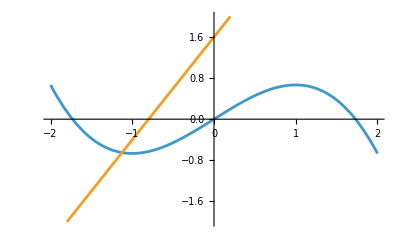

```mathematica
Plot[{δ v-v^3/3,(v+β)/γ},{v,-2,2},PlotRange->{-2,2}]
```

0.316503

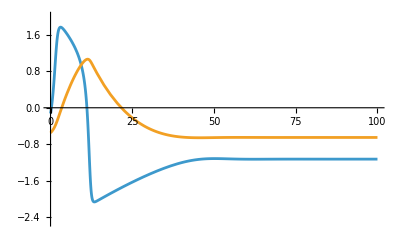

```mathematica
(*Simulacion de FHN ODE con la parametrizacion usual*)
eqn= FindRoot[δ v-v^3/3-(v+β)/γ==0,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;
Print[v0^2/4]
{V1,W1}=NDSolveValue[{v'[t]==δ v[t]-v[t]^3/3-w[t],w'[t]==ep(v[t] - γ w[t]+β),v[0]==v0+1,w[0]==w0+0.1},{v,w},{t,0,maxtime}];
Plot[{V1[t],W1[t]},{t,0,maxtime},PlotRange->{-2.5,2}]
```

```mathematica
(*Simulacion en parametrización centrada*)
A=(3v0+Sqrt[12 δ-3v0^2])/(6δ-6v0^2);
B=3A^3;
KK1=3A^2;
τ=1/(9 ep A^4);
α=-3 A v0 -1;
γt=γ Sqrt[ep τ];
Print["A=",A]
Print["α=",α]
{x1,y1}=NDSolveValue[{x'[t]==x[t](1-x[t])(x[t]-α)-y[t],τ y'[t]==x[t] - γt y[t],x[0]==A(V1[0]-v0),y[0]==B(W1[0]-w0)},{x,y},{t,0,maxtime/KK1}];
(*Plot[{x1[t],α},{t,0,maxtime/KK},PlotRange->{-0.5,1.2}]*)
Plot[{v0+(1/A)x1[t/KK1],w0+(1/B)y1[t/KK1]},{t,0,maxtime},PlotRange->{-2.5,2}]
```

A=0.320542

α=0.0819964

-Graphics-